### Инициализация

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;U0=0.01;
b=0.6;a=1; p0=P0=100000;
bx=1;by=1;
Pressure[x_,y_,a_,b_,P0_]=If[(x/a)^2+(y/b)^2≤1,Re[P0 √(1-(x/a)^2-(y/b)^2)],0];
Displacement[x_,y_,a_,b_,U0_]=If[(x/a)^2+(y/b)^2≤1,U0,0];
(*Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,P0,0];*)
s=1.5*a;(*размер расчетной области*)
(*Установить h = 3a/19 для n = 20*)
h= 3a /39;(*размер ГЭ*)
n=2 s/h+1(*number of elementary units*)
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];
Plot3D[Pressure[x,y,a,b,P0],{x,-s,s},{y,-s,s},AxesLabel->Automatic,PlotRange->All];
```

40.

### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(Subscript[x, 1] x2 (Subscript[x, 1]^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+Subscript[x, 1]) x2 ((-a+Subscript[x, 1])^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
σ1[x1_,x2_,x3_,a_,b_] =
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]);
```

## 1) Графики

### Графики напряжений

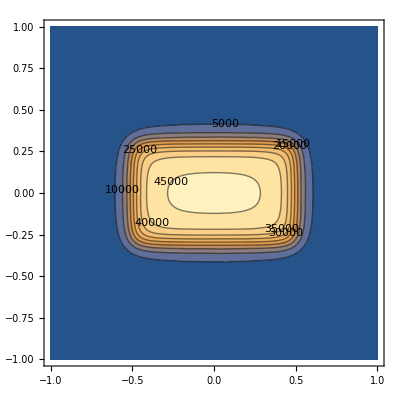

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

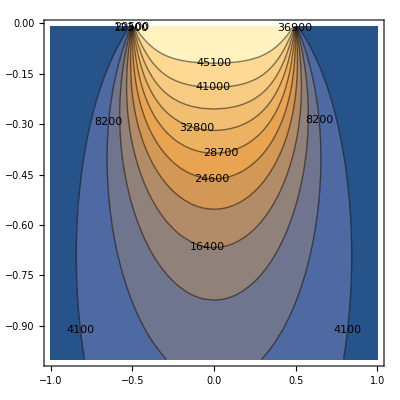

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

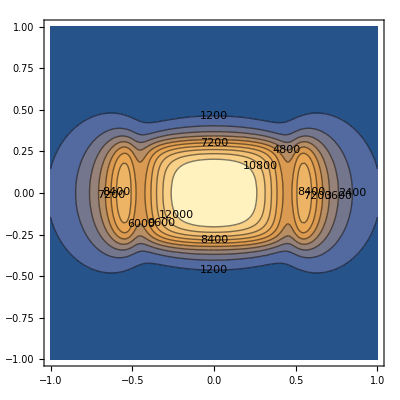

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

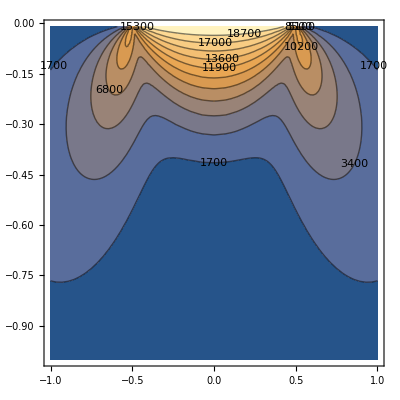

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

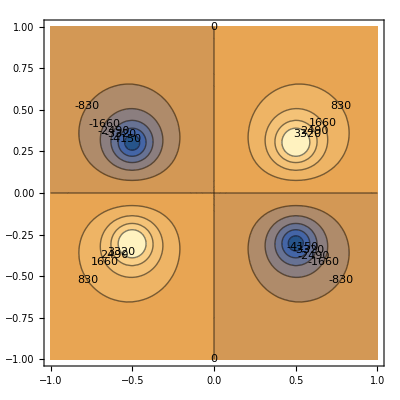

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

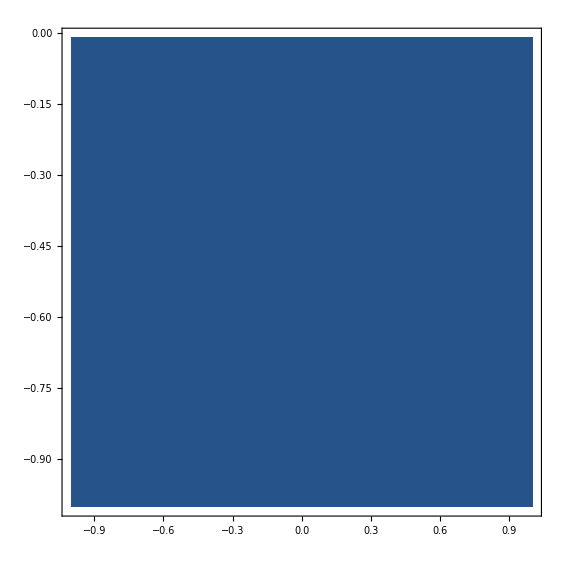

```mathematica
Print[ContourPlot[σ[1,2,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

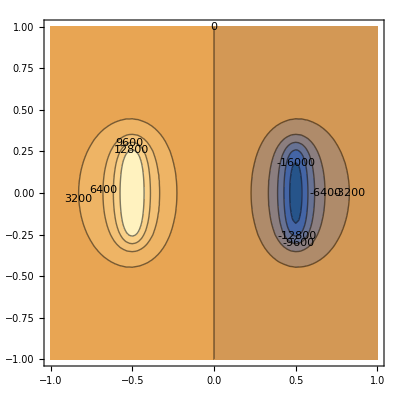

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

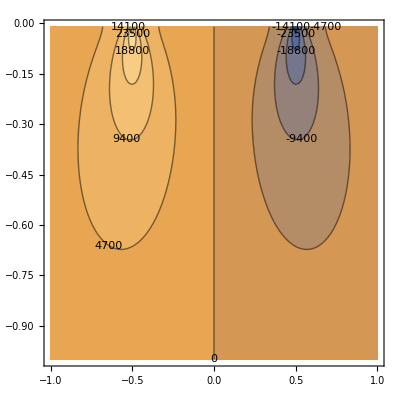

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

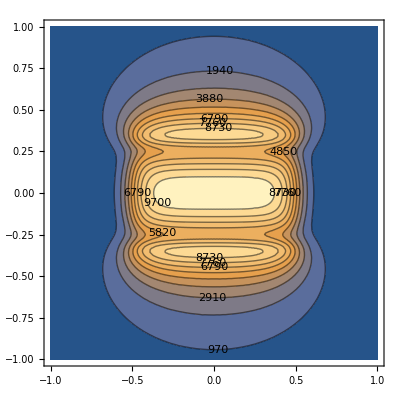

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

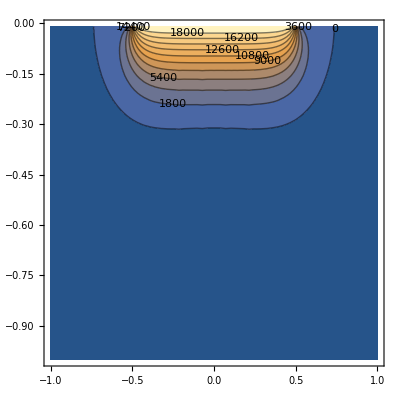

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

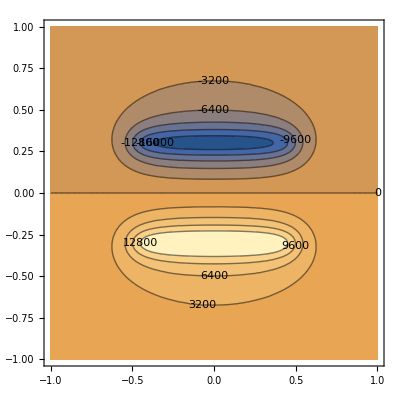

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

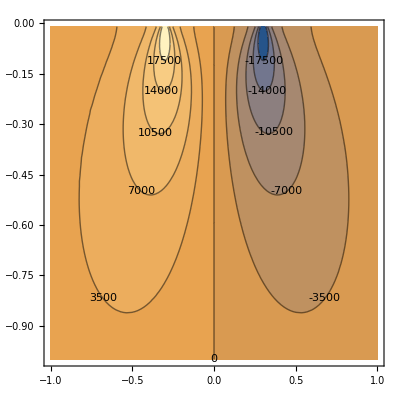

```mathematica
Print[ContourPlot[σ[2,3,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

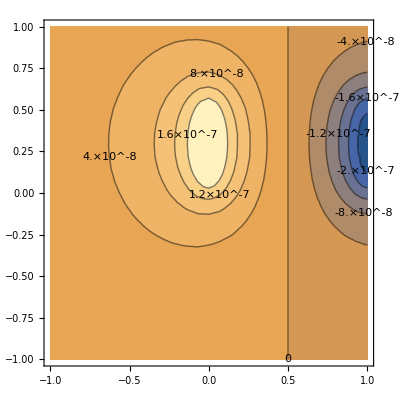

```mathematica
Print[ContourPlot[U[1,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

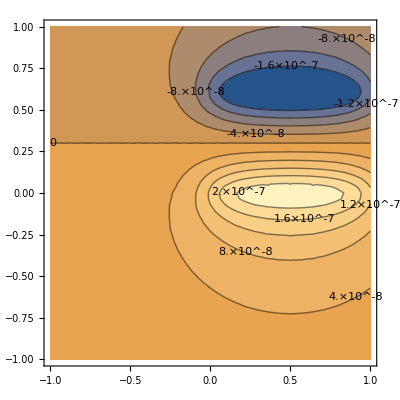

```mathematica
Print[ContourPlot[U[2,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

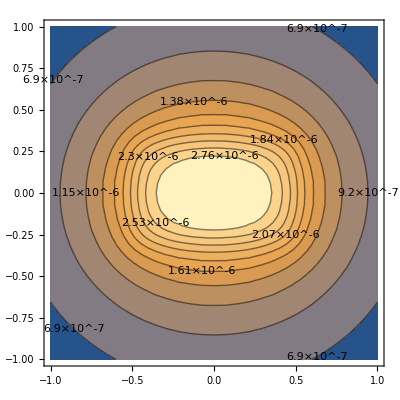

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

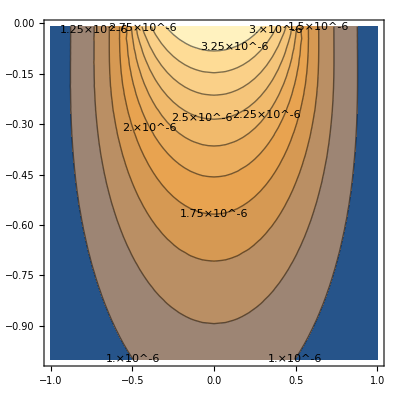

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

## 2) Граничная задача для вдавливания плоского эллиптического штампа

#### Графики функции поверхностного распределения и её дискретизации

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
ListPlot3D[DisplacementTab,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
BoundaryElements=Table[{X[[xi]],Y[[yj]],DisplacementTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
```

### Получение решения последовательно

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
(*PotV[xj_,yj_] =Sum[σ1[X[[m]]-xj,Y[[o]]-yj,-0.001,h,h]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}];
FPT=Flatten[PressureTab];*)
```

```mathematica
(*Equationq=Flatten[Table[PotV[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];*)
Equationq=Flatten[Table[Sum[U[3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,U0,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==DisplacementTab[[i,j]],{i,1,n},{j,1,n}]];
```

```mathematica
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntSRes:=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n U[3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*SolN1q[[i,j]]];
```

```mathematica
Resq=Table[DIntSRes[X[[i]],Y[[j]],U0],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*CUDAQ[] *)
```

```mathematica
(*CUDAResourcesInstall[]*)
```

```mathematica
(*Table[U[3,3][X[[i]]-X[[1]],h,Y[[i]]-Y[[1]],h,0.01,p0,λ,μ],{i,1,n},{j,1,n}]//MatrixForm*)
```

## 3)Перемещения внутри эллипса заданы

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];
(*Print["i: ",i," j: ",j]*)];

]]
Print["Amount of Boundary elements inside ellipse is: ",amount]
Ak = Table[Subscript[q, k],{k,1,amount}];
PotV[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,-0.01,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

Amount of Boundary elements inside ellipse is: 324

```mathematica
Equation2=Table[PotV[X[[Mp[[i,1]]]],Y[[Mp[[i,2]]]]]==U0,{i,1,amount}];
```

```mathematica
Solq = Solve[Equation2,Ak];
```

```mathematica
SolutionValues=Table[Solq[[1,i,2]],{i,1,amount}];
```

```mathematica
(*добавление столбца со значениями, выполнять только один раз*)
Tmp=Transpose[Mp];
AppendTo[Tmp,SolutionValues];
Mp=Transpose[Tmp];
```

```mathematica
FinalList=Table[0,{i,1,n},{j,1,n}];
```

```mathematica
Table[FinalList[[Mp[[i,1]],Mp[[i,2]]]]=Mp[[i,3]],{i,1,amount}];(*в необходимые места подставляем полученные значения, остальные приравниваем 0, для того, чтобы построить 3-х мерный график*)
FinalList//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.08653×10^-8 | 7.51956×10^-8 | -1.08112×10^-7 | 9.21384×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.30269×10^-8 | 4.25599×10^-8 | -2.56808×10^-8 | 21389.5 | -3731.1 | 21389.5 | -8.87138×10^-8 | 8.97679×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.80822×10^-8 | 3.91553×10^-8 | 21062.5 | -6469.55 | -4445.05 | -3976.18 | -4445.05 | -6469.55 | 21062.5 | 6.80247×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.50041×10^-8 | 20455.5 | -30558.1 | 24461.6 | -6039.39 | 21546.3 | -6039.39 | 24461.6 | -30558.1 | 20455.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -6.95038×10^-9 | 1.65322×10^-8 | -6850.12 | 25138.4 | -12178.8 | 39.58 | -9506. | 39.58 | -12178.8 | 25138.4 | -6850.12 | 7.58581×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.0894×10^-9 | 18300.4 | -2180.3 | -9215.44 | 2262.05 | 15468.3 | -586.302 | 15468.3 | 2262.05 | -9215.44 | -2180.3 | 18300.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -7.00929×10^-8 | 3.63191×10^-8 | -5458.63 | -3194.73 | 20682.1 | -8270.52 | -4322.2 | -5561.09 | -4322.2 | -8270.52 | 20682.1 | -3194.73 | -5458.63 | 1.49325×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.76115×10^-8 | 18358. | -3862.71 | 19057.9 | -30975.8 | 23642.8 | -6231.94 | 20818.1 | -6231.94 | 23642.8 | -30975.8 | 19057.9 | -3862.71 | 18358. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.07386×10^-7 | -4257.33 | -2675.95 | -6568.54 | 23694.3 | -11555.8 | -1269.99 | -8830.12 | -1269.99 | -11555.8 | 23694.3 | -6568.54 | -2675.95 | -4257.33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.48311×10^-8 | 1.35473×10^-7 | 16196.6 | -2423.64 | 17233.3 | -29408.2 | 21875.7 | -4636.81 | 19062.4 | -4636.81 | 21875.7 | -29408.2 | 17233.3 | -2423.64 | 16196.6 | -4.69989×10^-9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.71333×10^-8 | 18276.4 | -25633.1 | 18163.2 | -27677.7 | 44619.9 | -32626. | 19674.7 | -29892.3 | 19674.7 | -32626. | 44619.9 | -27677.7 | 18163.2 | -25633.1 | 18276.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.07682×10^-7 | -3283.72 | 18408.8 | -4983.02 | 19609. | -31910.8 | 24277.4 | -7126.6 | 21469.6 | -7126.6 | 24277.4 | -31910.8 | 19609. | -4983.02 | 18408.8 | -3283.72 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.03626×10^-7 | 17662.2 | -25339.5 | 17692.5 | -27317.3 | 44180. | -32250.1 | 19242.7 | -29513. | 19242.7 | -32250.1 | 44180. | -27317.3 | 17692.5 | -25339.5 | 17662.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -9.77601×10^-8 | -3497.96 | 18510.2 | -5158.24 | 19733.4 | -32073.2 | 24408.8 | -7285.3 | 21602.6 | -7285.3 | 24408.8 | -32073.2 | 19733.4 | -5158.24 | 18510.2 | -3497.96 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.75045×10^-8 | 17662.2 | -25339.5 | 17692.5 | -27317.3 | 44180. | -32250.1 | 19242.7 | -29513. | 19242.7 | -32250.1 | 44180. | -27317.3 | 17692.5 | -25339.5 | 17662.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.09842×10^-8 | -3283.72 | 18408.8 | -4983.02 | 19609. | -31910.8 | 24277.4 | -7126.6 | 21469.6 | -7126.6 | 24277.4 | -31910.8 | 19609. | -4983.02 | 18408.8 | -3283.72 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.84502×10^-8 | 18276.4 | -25633.1 | 18163.2 | -27677.7 | 44619.9 | -32626. | 19674.7 | -29892.3 | 19674.7 | -32626. | 44619.9 | -27677.7 | 18163.2 | -25633.1 | 18276.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.23386×10^-8 | 16196.6 | -2423.64 | 17233.3 | -29408.2 | 21875.7 | -4636.81 | 19062.4 | -4636.81 | 21875.7 | -29408.2 | 17233.3 | -2423.64 | 16196.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.6465×10^-8 | -4257.33 | -2675.95 | -6568.54 | 23694.3 | -11555.8 | -1269.99 | -8830.12 | -1269.99 | -11555.8 | 23694.3 | -6568.54 | -2675.95 | -4257.33 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.34233×10^-8 | 18358. | -3862.71 | 19057.9 | -30975.8 | 23642.8 | -6231.94 | 20818.1 | -6231.94 | 23642.8 | -30975.8 | 19057.9 | -3862.71 | 18358. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.9462×10^-8 | -5458.63 | -3194.73 | 20682.1 | -8270.52 | -4322.2 | -5561.09 | -4322.2 | -8270.52 | 20682.1 | -3194.73 | -5458.63 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.46382×10^-8 | 18300.4 | -2180.3 | -9215.44 | 2262.05 | 15468.3 | -586.302 | 15468.3 | 2262.05 | -9215.44 | -2180.3 | 18300.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2.47536×10^-8 | -6850.12 | 25138.4 | -12178.8 | 39.58 | -9506. | 39.58 | -12178.8 | 25138.4 | -6850.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2.24705×10^-8 | 20455.5 | -30558.1 | 24461.6 | -6039.39 | 21546.3 | -6039.39 | 24461.6 | -30558.1 | 20455.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.74075×10^-8 | 21062.5 | -6469.55 | -4445.05 | -3976.18 | -4445.05 | -6469.55 | 21062.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.31998×10^-8 | 21389.5 | -3731.1 | 21389.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ListPlot3D[FinalList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-